# Biology 101 - Lesson 03: The Recent Breakthrough

## Willem Nielsen

### The Recent Breakthrough

Okay so what is his new work?

For a long time, as mentioned, he spent more of his efforts on the developmental side of biology, rather than the evolutionary side. In attending biology conferences he would often think about what is the space of all possible rules like, and in NKS, in the context of discussing evolution, he actually noted that nearby rules did seem to have similar behavior:

```mathematica
IdentityCARule[k_Integer,r_Integer]:=Flatten[Table[Table[Table[i,{j,k^r}],{i,k-1,0,-1}],{m,k^r}]]

EvolveCARuleStep[rule_List,k_Integer,r_Integer,newnonid_:1,changenonid_:1,newid_:1]:=Module[{newrule=rule,id,pos,set,center=IdentityCARule[k,r],rand=RandomReal[{0,newnonid+changenonid+newid}]},id=Flatten[Position[Drop[MapThread[Equal,{center,rule}],-1],TrueQ[rand<newnonid]]];
If[Length[id]>0,pos=id⟦RandomInteger[{1,Length[id]}]⟧;set=If[rand<newnonid+changenonid,Complement[Range[0,k-1],If[rand<newnonid,{rule⟦pos⟧},{rule⟦pos⟧,center⟦pos⟧}]],{center⟦pos⟧}];If[Length[set]>0,newrule⟦pos⟧=set⟦RandomInteger[{1,Length[set]}]⟧]];newrule]

EvolveCARule[k_Integer,r_Integer,count_Integer,newnonid_:1,changenonid_:1,newid_:1]:=NestList[EvolveCARuleStep[#,k,r,newnonid,changenonid,newid]&,IdentityCARule[k,r],count]

EvolveCARuleGraphic[rule_,k_,r_,colormap_:{GrayLevel[0.85],GrayLevel[0],GrayLevel[0.4]}]:=Module[{center=IdentityCARule[k,r]},Graphics[{Table[If[rule⟦i⟧==center⟦i⟧,{Black,Point[{i+.5,.5}]},{colormap⟦rule⟦i⟧+1⟧,Rectangle[{i,0},{i+1,1}]}],{i,k^2 r+1}],Line[{{1,0},{1,1},{Length[rule]+1,1},{Length[rule]+1,0},{1,0}}],Table[Line[{{i,0},{i,1}}],{i,2,Length[rule]}]},ImageSize->110]]

BlockRandom[SeedRandom[245671,Method->"Legacy"];
T=Take[First/@Split[EvolveCARule[3,1,200,1,1,0.1]],54]];

leg=EvolveCARuleGraphic[#,3,1]&/@T;

rp=RulePlot[CellularAutomaton[{FromDigits[#,3],3,1}],CenterArray[{1,2,1},65],30,ImageSize->110]&/@T;

GraphicsGrid[Partition[MapThread[Labeled[#1,#2,ImageSize->110]&,{rp,leg}],6],ImageSize->{650, Automatic}]
```

-Graphics-

But, he never really had the intuition or motivation to think that this was worth exploring further.

That changed when he started doing more work on machine learning, both practically for the development of Wolfram Language (Mathematica), and scientifically in understanding how ChatGPT works. And in one of his posts on machine learning, in trying to answer the question, “Can one find a system that does X?” he attempted to compare what a neural network could achieve with what a random iterative search could achieve. This, in combination with hearing about his friend Greg Chaitlin’s work relating the Busy Beaver problem to evolution, he was motivated to try out some adaptive algorithms on cellular automata. More specifically, he tried “evolving” a cellular automata, by changing one rule at a time, to find a pattern that had a particular finite length:

And to his surprise, it actually worked, here is an example evolution to length 50:

```mathematica
deathdiff[rule_,t_:100,max_:150]:=With[{array=CellularAutomaton[rule,{{1},0},{max,All}]},Abs[LengthWhile[Reverse[array],Total[#]==0&]-(max-t)]]
```

```mathematica
randrulesx[rule_,n_Integer,k_:5]:=FromDigits[#,k]&/@With[{dig=IntegerDigits[rule,k,k^3]},Union[Table[ReplacePart[dig,RandomInteger[{1,Length[dig]-1}]->RandomInteger[{0,k-1}]],n]]]
```

```mathematica
Grid[Partition[Framed[ArrayPlot[CellularAutomaton[#,{{1},0},{55,{-14,14}}],GridLines->{None,{5}},
GridLinesStyle->Directive[Thickness[.015],GrayLevel[0,.8]],ColorRules->{0->White,1->Hue[0.08, 1, 1],2->Hue[0.75, 0.86, 0.8200000000000001],3->Hue[0.14, 0.81, 0.99]},
Frame->None,ImageSize->59],FrameStyle->GrayLevel[0, 0.3],FrameMargins->0]&/@(SeedRandom[7067];With[{k=3},
NestList[{First[First[SortBy[{#,deathdiff[{#,k,1},50,100]}&/@randrulesx[#[[1]],100,k],Last]]],k,1}&,
{k RandomInteger[k^k^3/k],k,1},20]]),10],Spacings->{.25,.25}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

This simple idea then blossomed into a bunch of new work in theoretical biology from Stephen in early 2024. From this model of evolution, there were many interesting experiments to try, conclusions to be drawn, and implications for biology to share. Before I get to those though, I should be more precise about how the “adaptive evolution” works.

Starting from the null rule, you make a single random change (mutation) to one rule in the automaton. If that rule, with an initial condition of a single red square, leads to a longer or equal length pattern (that is the number of steps until it goes to white), then you keep that change. Here’s what it looks like when we show successive changes to the ruleset, or “genotype”, that were kept:

```mathematica
e3 = Module[
{deep=5000,cut=200,ru,life},
SeedRandom[5000+53];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]];
```

```mathematica
keptrus = First/@Split[First/@e3];
```

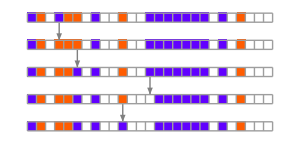
-Graphics-
⋮
-Graphics-
⋮

```mathematica
Column[{{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicates[keptrus][[1;;5]],(*"Arrows"->"Line",*)ImageSize->300],"⋮",{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicates[keptrus][[100;;104]],(*"Arrows"->"Line",*)ImageSize->300],"⋮"},Center]
```

And here is the “breakthrough phenotypes”, or steps in the evolution where a longer finite length (higher fitness) was achieved:

```mathematica
e3 = Module[
{deep=5000,cut=200,ru,life},
SeedRandom[5000+53];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]];
```

```mathematica
evo=Map[DeleteDuplicates,SplitBy[e3,Last]];
```

```mathematica
res=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,20(Length[data]+1)^.7},
Mesh->True,MeshStyle->Opacity[.1] ]]&,
evo,{2}];
```

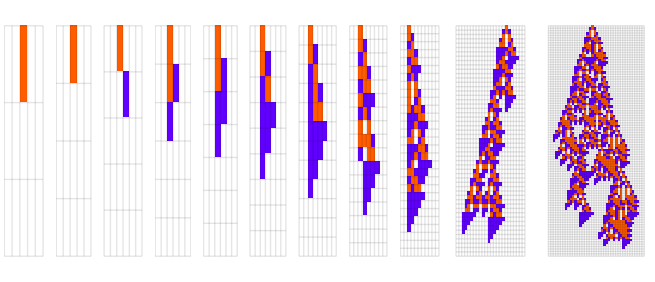

```mathematica
GraphicsRow[First/@res]
```

So already you can see the qualitative resemblance to biological evolution.

And the thing that is most striking about these patterns is their sheer complexity. In other words, the mechanisms that the pattern uses to achieve the “goal” of increasing finite lifetime, are very intricate and therefore difficult to explain. Thus, in many cases, the best we can do in answering the question of why this particular pattern was “selected”, will be to say, “because it was”.

And in fact, running more evolutions, we see that in each case, very different underlying mechanisms are used, which suggests that most of the details of the pattern are not a result of the selection process, but rather just happened to have occurred in that particular evolutionary path:

```mathematica
es = Module[
{deep=5000,cut=200,ru,life},
SeedRandom[5000+#];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]]&/@ {54, 60, 16};
```

```mathematica
evos=Map[DeleteDuplicates,SplitBy[#,Last]]&/@es;
```

```mathematica
ress=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,20(Length[data]+1)^.7} ]]&,
#,{2}]&/@ evos;
```

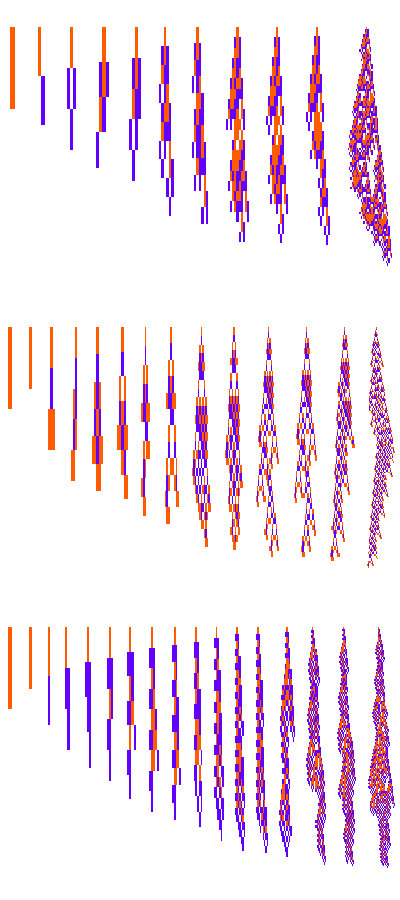

```mathematica
Column[GraphicsRow[First/@#]&/@ Prepend[ress[[;;-2]], ress[[-1]]]]
```

And Stephen shows that this is quite a general phenomena. Looking at different rule spaces, for example, we see more of the same, here is the k = 4, r = 1 case:

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
evos = Module[
{deep=2000,cut=200,ru,life,evo,data},
SeedRandom[426778+#];
evo=NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep]
]&/@ {181, 43};
```

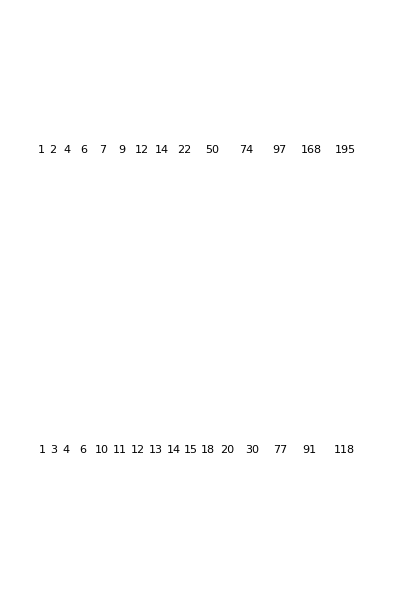

```mathematica
Column[GraphicsRow[Labeled[{{"[◼]", "PlotCA"}}[First[#],"Trim"->{1,5},ImageSize->{Automatic,22.5 Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@Rest[#[[ResourceFunction["ProgressiveMaxPositions"][#[[All,-1]]]]]]]&/@ evos]
```

Or the two-dimensional case, where we also see considerable complexity:

```mathematica
allrules=;
```

```mathematica
Row[Labeled[ArrayPlot3D[CellularAutomaton[<|"RuleNumber"->#[[1,1]],"Neighborhood"->9,"Dimension"->2,"Colors"->2|>,{CrossMatrix[1],0},#[[1,2]]],Method->{"ShrinkWrap"->True},ImageSize->{Automatic,22(#[[1,2]])^.5},Lighting->,ColorRules->{1->Hue[0.06, 0.93, 0.96]},Mesh->None],Text[Style[#[[1,2]]-1,Small]]]&/@allrules[[190]]]
```

-Graphics3D-0-Graphics3D-1-Graphics3D-3-Graphics3D-4-Graphics3D-6-Graphics3D-12-Graphics3D-14-Graphics3D-49-Graphics3D-93-Graphics3D-145-Graphics3D-147-Graphics3D-163-Graphics3D-166-Graphics3D-235

Or even with different fitness functions, here we’re selecting for wider patterns instead of longer:

```mathematica
Module[{
k=3,r=1,cut=800,deep=5000,fun=Length@*First,
init,evo,ru,data,lt,test,mask,canonical,res},
res=[[;;3]];
res=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,Min[20(Length[data]+1)^.7,600]}]]&,
res,{2}];
GraphicsColumn[GraphicsGrid[{#}]&/@res,Automatic,0]
]
```

-Graphics-

Or aspect ratio, here are some results of searching for a pattern that has a 3:1 aspect ratio:

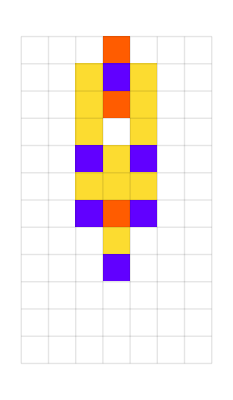
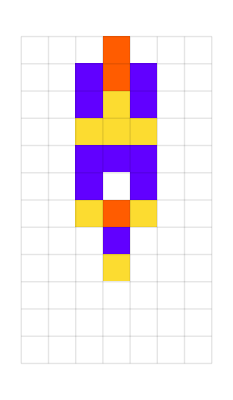
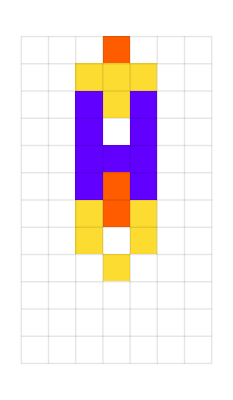
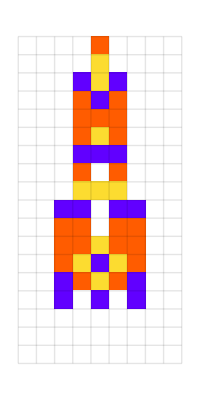
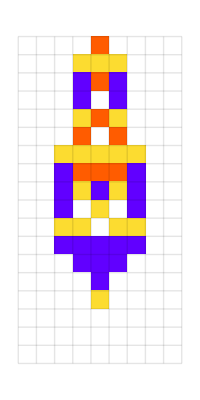
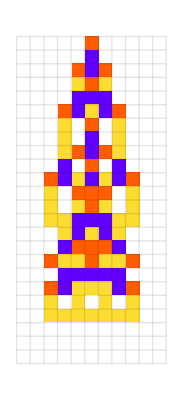
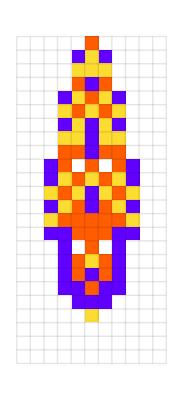
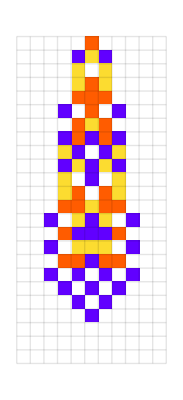
{-Graphics-{9,3},-Graphics-{9,3},-Graphics-{9,3},-Graphics-{15,5},-Graphics-{15,5},-Graphics-{21,7},-Graphics-{21,7},-Graphics-{21,7},-Graphics-{21,7},-Graphics-{21,7},-Graphics-{27,9},-Graphics-{27,9},-Graphics-{39,13},-Graphics-{45,15},-Graphics-{51,17},-Graphics-{57,19},-Graphics-{57,19},-Graphics-{69,23},-Graphics-{69,23},-Graphics-{111,37}}

```mathematica
Style[With[{data=CellularAutomaton[
#[[1]],{{1},0},#[[2,1]]+2]},
Labeled[ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,24Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
],Style[#[[2]],"Text",Italic,Gray,11]]]&/@{{{109636419052937157723438118980837975564,4,1},{9,3}},{{232259557841861635493049224869714791688,4,1},{9,3}},{{338236923684700346441755364009144414988,4,1},{9,3}},{{3663450190864856052378894455912568704,4,1},{15,5}},{{136651796051772457646439217666630305548,4,1},{15,5}},{{74948306682547943335519680440646385168,4,1},{21,7}},{{193464179513193600562914906378802444040,4,1},{21,7}},{{193649253952380488246394671786963518216,4,1},{21,7}},{{298798483958213368517806363132769509688,4,1},{21,7}},{{337623673395850352619393223745807586160,4,1},{21,7}},{{143430394600545658197868087730119774096,4,1},{27,9}},{{246493520306698100424983701858655419148,4,1},{27,9}},{{180664442152675280322045408237394267792,4,1},{39,13}},{{36324902254124465598971313626629143056,4,1},{45,15}},{{289850694849104464885050820643032709680,4,1},{51,17}},{{143923012087109979886256736424975337072,4,1},{57,19}},{{280384207228392989942672757173339297804,4,1},{57,19}},{{283391784414472610606660051001734099568,4,1},{69,23}},{{330335253914559274144004959766636949128,4,1},{69,23}},{{142140648448642989785750794400464692296,4,1},{111,37}}},LineSpacing->{1.1,0}]
```

So the claim is that natural selection in biology works similarly to these cases in the sense that evolution selects organisms based on some high-level metric of fitness. But, because biological systems are capable of arbitrarily complex behavior (just like our automata), the processes used to satisfy the fitness functions will be full of irreducibility.

In Stephen’s language, evolution is like a computationally-bounded observer of computationally unbounded processes.

In NKS, Stephen had models for subsystems within biology, like pigmentation, growth and shape. And with these models he showed that much of the variation and complexity of these subsystems arose as a consequence of computational irreducibility.

With these new adapted cellular automata, he now has a generalized model for all biological processes, not just pigmentation, growth and shape. And with this more abstract model, he can provide a clearer picture for the behavior of biological processes in general.

And as we’ve seen, these pictures strongly suggest once again that the dominant force in biological systems is computational irreducibility and not natural selection.

Okay, so what else can we takeaway from this new model?

So far, we’ve been discussing the individual patterns, but what about the space of all possible patterns?

Well, we can actually draw a “fitness landscape” by showing the graph of all possible rules:

```mathematica
Module[{mg,lifetimes,g1,g2,emb,toRule,fromRule,lp3},
mg={{"[◼]", "MutationGraph"}}[2,3/2];
lifetimes=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2]][[2,1,1]];
g1=GridGraph[Table[2,15]];
emb=GraphEmbedding[g1];
g2=NearestNeighborGraph[Tuples[{1,0},15],
VertexCoordinates->Automatic];
toRule=Map[FromDigits[Append[#,0],2]&,
FindGraphIsomorphism[g1,g2][[1]]];
fromRule=Association[Map[Reverse,
Normal[toRule]]];
emb=Association[FilterRules[
Thread[Lookup[toRule,VertexList[g1]]->emb],
VertexList[mg]]];
g1=Graph[mg,VertexCoordinates->Normal[emb]];
lp3=ListPointPlot3D[MapThread[Append,
{GraphEmbedding[g1],Lookup[lifetimes,VertexList[g1]]}],
PlotRange->All,ColorFunction->(Blend[
RGBColor/@{{"[◼]", "CustomStyleData"}}["Landscape"],#3]&),
Ticks->None,PlotStyle->EdgeForm[White]];
lp3=ReplaceRepeated[lp3,Point[x_]:>{Ellipsoid[x,1.2{.05,.05,.07/.6}]}];
g1=Graph3D[g1,VertexStyle->Opacity[0],VertexSize->0,
EdgeStyle->Directive[GrayLevel[.4,.15],Thickness[.0015]],
VertexCoordinates->MapThread[Append,
{GraphEmbedding[g1],Lookup[lifetimes,VertexList[g1]]}]];
Show[lp3,g1,BoxStyle->Opacity[.4],Axes->None,
PlotRange->CoordinateBounds[GraphEmbedding[g1]],
BoxRatios->{1,1,.6},ViewPoint->{1.25,-2.90,1.19},
ViewVector->{{12.87,-15.33,16.21},{3.93,3.18,5.5}},
ViewVector->{0,0,1}]
]
```

-Graphics3D-

Here the height corresponds to the length of the automata or “fitness”. And the goal of adaptive evolution is thus to trace a never go down path in this landscape:

```mathematica
Module[{mg,lifetimes,g1,g2,emb,toRule,fromRule,lp3,
deep=150,cut=200,ru,life,evo,line
},
SeedRandom[920384];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,{1,1,1,0,1,1,1},cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,2,3/2},1},deep];
mg={{"[◼]", "MutationGraph"}}[2,3/2];
lifetimes=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2]][[2,1,1]];
g1=GridGraph[Table[2,15]];
emb=GraphEmbedding[g1];
g2=NearestNeighborGraph[Tuples[{1,0},15],
VertexCoordinates->Automatic];
toRule=Map[FromDigits[Append[#,0],2]&,
FindGraphIsomorphism[g1,g2][[1]]];
fromRule=Association[Map[Reverse,
Normal[toRule]]];
emb=Association[FilterRules[
Thread[Lookup[toRule,VertexList[g1]]->emb],
VertexList[mg]]];
g1=Graph[mg,VertexCoordinates->Normal[emb]];
line=Graphics3D[{Thickness[.01],Red,
Line[
Append[emb[#[[1,1]]],#[[2]]-1]&/@First/@Split[evo]
],
Ellipsoid[Append[emb[#[[1,1]]],#[[2]]-1],2{.05,.05,.07/.6}
]&/@First/@Split[evo]}];
lp3=ListPointPlot3D[MapThread[Append,
{GraphEmbedding[g1],Lookup[lifetimes,VertexList[g1]]}],
PlotRange->All,ColorFunction->(Opacity[.25,Blend[
RGBColor/@{{"[◼]", "CustomStyleData"}}["Landscape"],#3]]&),
Ticks->None,(*Filling->Bottom,*)PlotStyle->EdgeForm[White]];
lp3=ReplaceRepeated[lp3,Point[x_]:>{Ellipsoid[x,1.2{.05,.05,.07/.6}]}];
g1=Graph3D[g1,VertexStyle->Opacity[0],VertexSize->0,
EdgeStyle->Directive[Opacity[.05],Gray],
VertexCoordinates->MapThread[Append,
{GraphEmbedding[g1],Lookup[lifetimes,VertexList[g1]]}]];
Show[lp3,g1,line,BoxStyle->Opacity[.4],Axes->None,
PlotRange->CoordinateBounds[GraphEmbedding[g1]],
BoxRatios->{1,1,.6},ViewPoint->{1.25,-2.90,1.19},
ViewVector->{{12.87,-15.33,16.21},{3.93,3.18,5.5}},
ViewVector->{0,0,1}]
]
```

-Graphics3D-

And from this, we can get a sense of what is required for evolution to work. First, there needs to be enough dimensionality in the landscape. Now, actual genomes are way bigger than the number of rules we have here, so that isn’t an issue. Second, the “viable nodes” defined by the fitness function need to be numerous enough so that we don’t get stuck.

But these criteria alone aren’t enough because we could presumably have all the fit nodes cluster in one area. And the key point is that because of computational irreducibility, this won’t happen, and the nodes will be spread out enough so that we can indeed find an evolutionary path.

And this allows us to see how biological systems can navigate their complicated fitness landscapes, and make progress towards some high-level fitness function.

Similarly, because of the simplicity of the model, we can actually draw the multiway graph of all viable patterns (for the k = 2, r = 3/2 rule space):

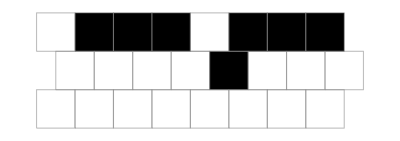
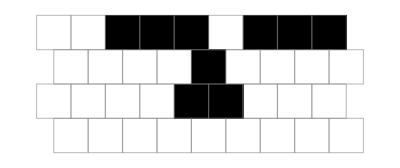
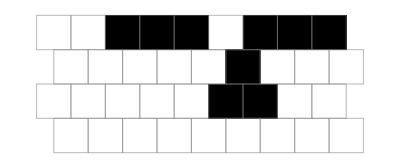
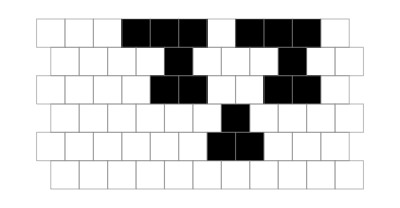
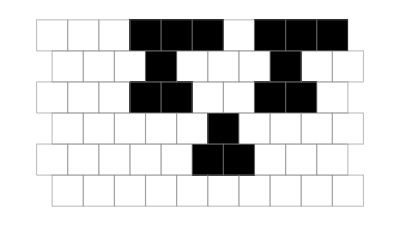
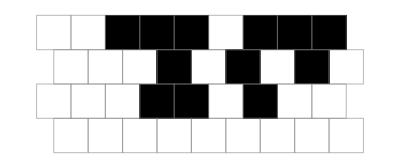
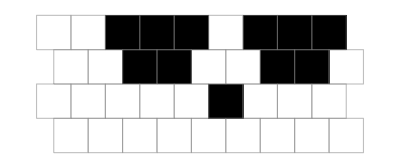
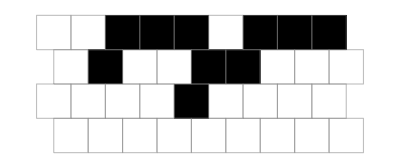

```mathematica
Module[{res,sublevels,vfs},
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
"SubLevels"];
sublevels=res[[2,1,1]];
res=res[[1]];
vfs=Association[KeyValueMap[Function[{key,rules},key->
{{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{Automatic,(2+key[[1]])10}]
&@First[Union[CellularAutomaton[{#,2,3/2},{{1,1,1,0,1,1,1},0},
key[[1]]]&/@rules]]
],sublevels]];
Graph[res,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->2/3,
EdgeStyle->Gray,
VertexSize->1/2,
VertexShapeFunction->Function[
Inset[vfs[#2],#1,Automatic,
Times[#3[[1]],
#/Last[#]&@ImageDimensions[vfs[#2]],
Sqrt[First[#2]+5]
]
]
],
PerformanceGoal->"Quality"
]
]
```

And from this, interestingly, we can see our model’s version of discrete branches in the tree of life.

Zooming out further, we can look at this multiway graph (in the larger symmetric k = 2, r = 2 rule space), but instead of just one fitness-function, we can compare two different fitness functions:

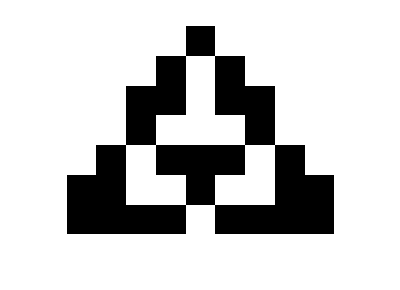
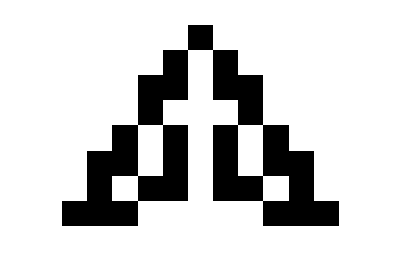
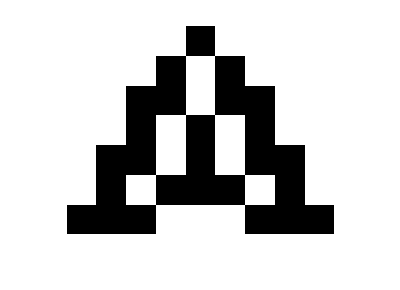
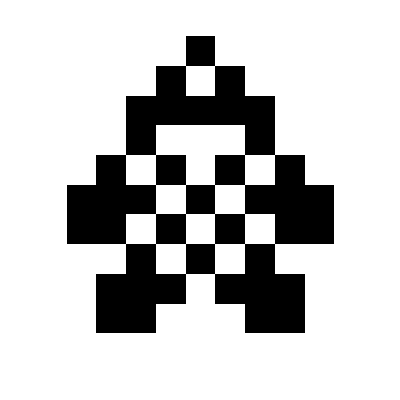
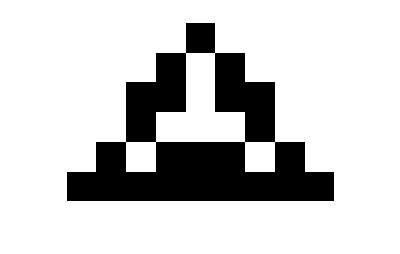
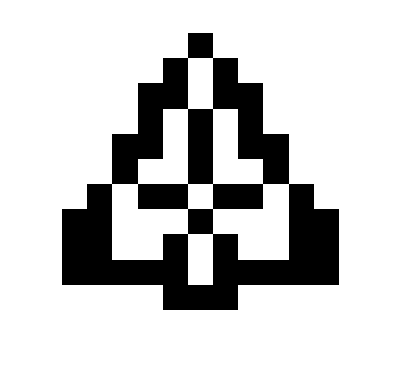
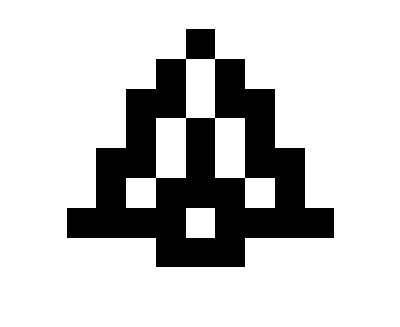
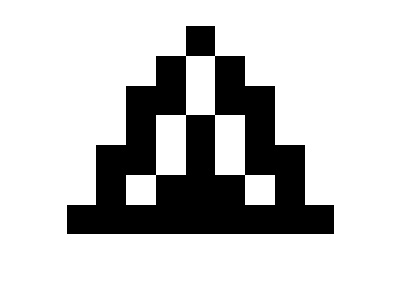

```mathematica
Module[{g1},
g1=VertexOutComponentGraph[{{"[◼]", "EvolutionaryMultiwayGraph"}}[{
{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],
{{"[◼]", "changeFitness"}}[{2,2},{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],
Length@*First]},
GraphLayout->"LayeredDigraphEmbedding",
"Reduced"->False,
AspectRatio->1,
EdgeStyle->{x_:>Association[
{1}->Directive[Hue[0.45, 0.54, 0.74],Thick,Opacity[8]],{2}->Directive[Hue[0.06, 0.96, 0.98],Thick,Opacity[8]],
{1,2}->Directive[{Hue[0.6,0.3,0.5,.35]}]
][Last[x]]}
],{{0,65815}}];
Legended[{{"[◼]", "addVertexFigures"}}[g1,{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],{2,2},
"VertexFigures"->1,VertexSize->1.2,AspectRatio->.7,ImageSize->550],LineLegend[{Directive[Hue[0.45, 0.54, 0.74],Thick,Opacity[8]],Directive[Hue[0.06, 0.96, 0.98],Thick,Opacity[8]],Directive[{Hue[0.6,0.5,0.5,.6]}]},{"height","width","both"}]]]
```

And so what we’re starting to see, is that we can view evolution as acting as a computationally bounded observer, selecting particular slices of the rule space. And Stephen then connects this idea to observers in physics, suggesting that much like there is the Second Law of Thermodynamics, there might also be similar high-level laws for the macroscopic “flow of evolution”.